```mathematica
ClearAll["Global`*"];
```

## Memory from BOB model

```mathematica
(*Computing the final spin of the blackholes*)
p0 = 0.04826; p1=0.01559; p2 = 0.00485; s4 = -0.1229; s5 = 0.4537; t0 = -2.8904; t2 = -3.5171; t3 = 2.5763; q=1; eta = 1/4; theta = π/2; 
pct= 0.99; tcut = 200; tmin = -20; tmax = 50;
```

```mathematica
Mf[α1_, α2_]:= 1- p0 - p1 (α1+ α2) - p2(α1+ α2)^2
αb[α1_, α2_]:= (q^2 α1+ α2)/(q^2+1)
```

```mathematica
Alpha[α1_, α2_]:= αb[α1, α2] + s4 eta  αb[α1, α2]^2 + s5 eta^2 αb[α1, α2]  + t0 eta αb[α1, α2]  + 2 √3 eta +  t2 eta^2 + t3 eta^3
```

```mathematica
(*ISCO calcualtion*)
Z1[af_]:= 1 + (1-af^2)^(1/3)((1+af)^(1/3) + (1-af)^(1/3))
Z2[af_, Z1_]:= √(3 af^2 + Z1^2)
RISCO[Z1_, Z2_]:= 3 + Z2 - √((3-Z1)(3+ Z1 + 2 Z2))
OMISCO[RISCO_, af_]:= 1/(RISCO^(3/2)+ af )
OMQNM[α1_, α2_]:= (1- 0.63 (1-αb[α1, α2])^0.3)/(2Mf[α1, α2])
```

```mathematica
(*BOB memory calculation*)
Y20[θ_]:=1/4 √(15/(2 π))Sin[θ]^2
Q[af_] := 2 (1-af)^-0.45
```

```mathematica
TAO[α1_, α2_]:= 2 Q[αb[α1, α2]]Mf[α1, α2]/(1- 0.63 (1-αb[α1, α2])^0.3)
```

```mathematica
Ap[α1_, α2_] := 1.068(1-Mf[α1, α2])^0.8918
OMREF[α1_, α2_]:= OMISCO[RISCO[Z1[αb[α1, α2]], Z2[αb[α1, α2], Z1[αb[α1, α2]]]], αb[α1, α2]]
```

```mathematica
OMP[α1_, α2_]:= ((OMQNM[α1, α2]^4 + OMREF[α1, α2]^4)/2)^(1/4)
OMM[α1_, α2_]:= ((OMQNM[α1, α2]^4 - OMREF[α1, α2]^4)/2)^(1/4)
```

```mathematica
(*Slight consusion over sign*)
KAPPAM[α1_, α2_]:= ((OMP[α1, α2]^4 + OMM[α1, α2]^4))^(1/4)
KAPPAP[α1_, α2_]:= ((OMP[α1, α2]^4 - OMM[α1, α2]^4))^(1/4)
(*BOB Memory*)
OM[t_, α1_, α2_]:= (OMP[α1, α2]^4 + OMM[α1, α2]^4 Tanh[t/TAO[α1, α2]])^(1/4)
```

```mathematica
MEMBOB[t_, α1_, α2_]:= (Sin[theta]^2)((17 + (Cos[theta])^2)/192/π)Ap[α1, α2]^2 TAO[α1, α2]OM[t, α1, α2]^2/OMM[α1, α2]^4
```

```mathematica
BOBmemScale[scale_]:= Plot[MEMBOB[t, scale, scale]-MEMBOB[-500, scale, scale], {t, -100, 50}, PlotRange->{{-100, 50},{0.0, 0.1}}]
```

```mathematica
Manipulate[BOBmemScale[n], {n, -0.9, 0.9}]
```

```mathematica
BOBmemScale2[scale1_, scale2_]:= Plot[MEMBOB[t, scale1, scale2]-MEMBOB[-500, scale1, scale2], {t, -100, 50}, PlotRange->{{-100, 50},{0.0, 0.1}}]
```

```mathematica
Manipulate[BOBmemScale2[a, b], {a, -0.9, 0.9}, {b, -0.9, 0.9}]
```

```mathematica
Eqn[α1_, α2_]:= NDSolve[{h'[t]==MEMBOB[t, α1, α2]-MEMBOB[-500, α1, α2], h[0]==0},h, {t, -60,40}]
```

```mathematica
Inthmem[scale_] := Plot[{Evaluate[h[t]/.Eqn[scale,scale]]}, {t,-40,40}, PlotRange->{{-40, 40},{-1.0,2.0}}]
```

```mathematica
Manipulate[Inthmem[n] , {n, -0.9, 0.9}]
```

```mathematica
Res[t_, α1_, α2_] :=h[t] /. Eqn[α1, α2]
```

```mathematica
generateBOBmemdata[α1_, α2_, ti_, tf_, dt_]:=Res[#, α1, α2]& /@ Range[ti, tf, dt]
```

```mathematica
dataBoBmem[α1_, α2_, ti_, tf_, dt_] :=Transpose@{Range[ti, tf, dt], generateBOBmemdata[ α1, α2, ti, tf, dt][[All, 1]]}
```

```mathematica
parabolaBoBmem[ t_, α1_, α2_, ti_, tf_, dt_]:=Fit[dataBoBmem[α1, α2, ti, tf, dt],{1,x,x^2},x]/.x-> t;
```

```mathematica
ResMquad[t_, α1_, α2_, ti_, tf_, dt_] := Res[t, α1, α2] - parabolaBoBmem[t, α1, α2, ti, tf, dt]
```

```mathematica
ResFinal[ α1_, α2_, ti_, tf_, dt_] :=Part[ResMquad[#, α1, α2, ti, tf, dt]& /@ Range[ti, tf, dt],  All, 1]
```

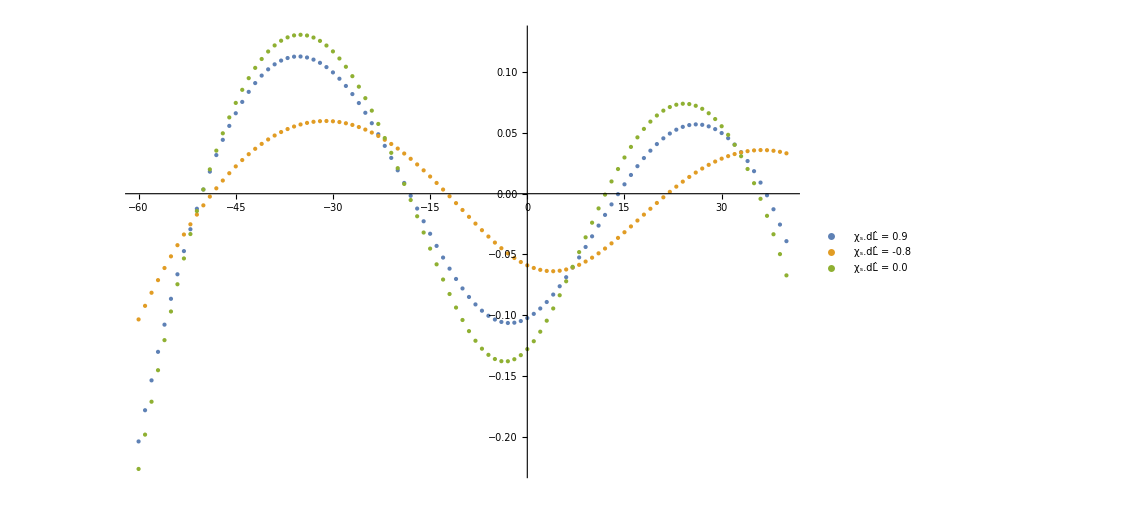

```mathematica
ListPlot[{Transpose@{Range[-60, 40, 1],ResFinal[ 0.9, 0.9, -60,40,1 ]},  Transpose@{Range[-60, 40, 1],ResFinal[ -0.8,-0.8, -60, 40, 1 ]},  Transpose@{Range[-60, 40, 1],ResFinal[ 0,0, -60, 40, 1 ]}},PlotLegends->Placed[{"χ_s.dL̂ = 0.9", "χ_s.dL̂ = -0.8","χ_s.dL̂ = 0.0"},{0.220,0.27}], BaseStyle->{FontFamily->"TeX", FontSize->23.5, LegendMarkerSize-> 30}, PlotStyle->PointSize[Large]]
```

```mathematica
DataResS0= Transpose@{Range[-60, 40, 1],ResFinal[ 0.0, 0.0, -60, 40,1 ]};
DataResS0p9= Transpose@{Range[-60, 40, 1],ResFinal[ 0.9, 0.9, -60, 40,1 ]};
DataResSm0p8= Transpose@{Range[-60, 40, 1],ResFinal[ -0.8, -0.8, -60, 40,1 ]};
```

```mathematica
PolyfitDataResS0 = Fit[DataResS0, {1, x, x^2, x^3, x^4, x^5, x^6, x^7},x];
PolyfitDataResS0p9 = Fit[DataResS0p9, {1, x, x^2, x^3, x^4, x^5, x^6, x^7},x];
PolyfitDataResSm0p8 = Fit[DataResSm0p8, {1, x, x^2, x^3, x^4, x^5, x^6, x^7},x];
```

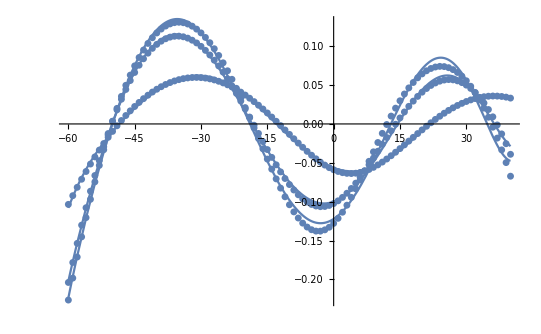

```mathematica
Show[ListPlot[DataResS0], Plot[PolyfitDataResS0, {x, -60 , 40}],ListPlot[DataResS0p9], Plot[PolyfitDataResS0p9, {x, -60 , 40}],ListPlot[DataResSm0p8], Plot[PolyfitDataResSm0p8, {x, -60 , 40}]]
```

```mathematica
(*Define Resedual function using polynomial fit*)
PolyResS0[t_]:= PolyfitDataResS0/.x-> t
PolyResS0p9[t_]:= PolyfitDataResS0p9/.x-> t
PolyResSm0p8[t_]:= PolyfitDataResSm0p8 /.x-> t
```

```mathematica
(*Define function to take nonzero value only insude the observation time*)
ResS0[t_, ti_, tf_]:= Piecewise[{{PolyResS0[t], ti≤ t ≤tf}}, 0]
ResS0p9[t_, ti_, tf_]:= Piecewise[{{PolyResS0p9[t], ti≤ t ≤tf}}, 0]
ResSm0p8[t_, ti_, tf_]:= Piecewise[{{PolyResSm0p8[t], ti≤ t ≤tf}}, 0]
```

```mathematica
(*Taking analytical fourier transform *)
FTS0I1[ω]= SetPrecision[Simplify[FourierTransform[ResS0[t, -35, 35], t, ω]Conjugate[FourierTransform[ResS0[t, -35, 35], t, ω]]//ComplexExpand], 40];
FTS0p9I1[ω]= Simplify[FourierTransform[ResS0p9[t, -35, 35], t, ω]Conjugate[FourierTransform[ResS0p9[t, -35, 35], t, ω]]//ComplexExpand];
FTSm0p8I1[ω]= Simplify[FourierTransform[ResSm0p8[t, -35, 35], t, ω]Conjugate[FourierTransform[ResSm0p8[t, -35, 35], t, ω]]//ComplexExpand];
```

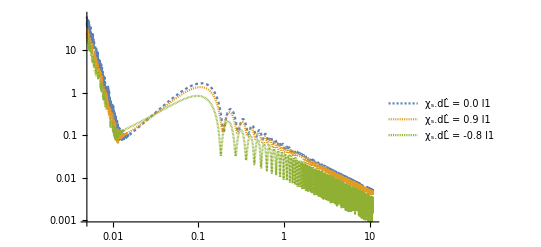

```mathematica
LogLogPlot[{Sqrt[Abs[FTS0I1[ω]]],Sqrt[Abs[FTS0p9I1[ω]]], Sqrt[Abs[FTSm0p8I1[ω]]] }, {ω, 0.005, 10.9}, PlotLegends->Placed[{"χ_s.dL̂ = 0.0 I1", "χ_s.dL̂ = 0.9 I1","χ_s.dL̂ = -0.8 I1"},{0.850,0.7}],PlotStyle-> {Dashing[0.005],Dashing[0.002], Dashing[0.001]} , WorkingPrecision->MachinePrecision]
```

```mathematica
Gf[f_, n_]:= (-1)^n √(2/π)(I)^n D[Sin[f]/f, {f,n}]
```

```mathematica
PNt[a_, nf_]:= Sum[a[[n+1]] x^n, {n, 0, nf}]
Cf[f_, n_]:= (-1)^n √(2/π)(I)^n D[Sin[f]/f, {f,n}]
PNf[a_, nf_]:= Sum[a[[n+1]]Cf[f, n], {n, 0, nf}]
```

```mathematica
PolyResS0[t]
```

-0.122172+0.00367111 t+0.000604845 t^2-5.52516×10^-6 t^3-5.40635×10^-7 t^4-7.23933×10^-10 t^5+1.40426×10^-10 t^6+1.20037×10^-12 t^7

```mathematica
PNt[CoefficientList[PolyResS0[t], t], 7]
```

-0.122172+0.00367111 x+0.000604845 x^2-5.52516×10^-6 x^3-5.40635×10^-7 x^4-7.23933×10^-10 x^5+1.40426×10^-10 x^6+1.20037×10^-12 x^7

```mathematica
FullSimplify[PNf[CoefficientList[PolyResS0[t],t], 7]Conjugate[PNf[CoefficientList[PolyResS0[t],t], 7]]//ComplexExpand]
```

1/f^16(1.16505×10^-17+3.58851×10^-15 f^2+7.0989×10^-13 f^4+f^6 (1.1548×10^-10+f ((0.-2.01948×10^-28 ⅈ)+f (1.79959×10^-8+f ((0.-2.58494×10^-26 ⅈ)+1.54843×10^-6 f+0.0000979115 f^3+(0.+2.11758×10^-22 ⅈ) f^4+0.00470845 f^5))))+(-1.16505×10^-17-3.56521×10^-15 f^2-7.02721×10^-13 f^4-1.14063×10^-10 f^6-1.77654×10^-8 f^8-1.5282×10^-6 f^10-0.0000968284 f^12-0.0046999 f^14) Cos[2 f]+f (-2.3301×10^-17-7.16148×10^-15 f^2-1.415×10^-12 f^4-2.30015×10^-10 f^6-2.79919×10^-8 f^8-2.08245×10^-6 f^10-0.000101981 f^12) Sin[2 f])

```mathematica
(*Try anlytical fourier transform method on trial functions (True )*)
```

```mathematica
CfTrial = {1,-1,1,-1,1};
```

```mathematica
PNTrial[a_, nf_, ti_, tf_]:= Piecewise[{{Sum[a[[n+1]] t^n, {n, 0, nf}], ti≤ t ≤tf }}, 0]
```

```mathematica
PNTrial[CfTrial, 3, -1, 1]
```

Piecewise[{{1-t+t^2-t^3, -1≤t≤1}, {0, True}}]

```mathematica
FourierTransform[PNTrial[CfTrial,1, -1, 1], t, f]
```

(2 ⅈ f Cos[f]+2 (-ⅈ+f) Sin[f])/(f^2 √(2 π))

```mathematica
(*Applying analytical fourier transform method to Reseduals*)
```

```mathematica
ResS0Coeff = CoefficientList[PolyResS0[t], t];
ResS0p9Coeff = CoefficientList[PolyResS0p9[t], t];
ResSm0p8Coeff = CoefficientList[PolyResSm0p8[t], t];
```

```mathematica
PNfSpin[a_, nf_, ti_, tf_]:= Sum[SetPrecision[a[[n+1]](-1)^n √(2/π)(I)^n D[Sin[f(tf-ti)/2]/f, {f,n}], 40], {n, 0, nf}]
```

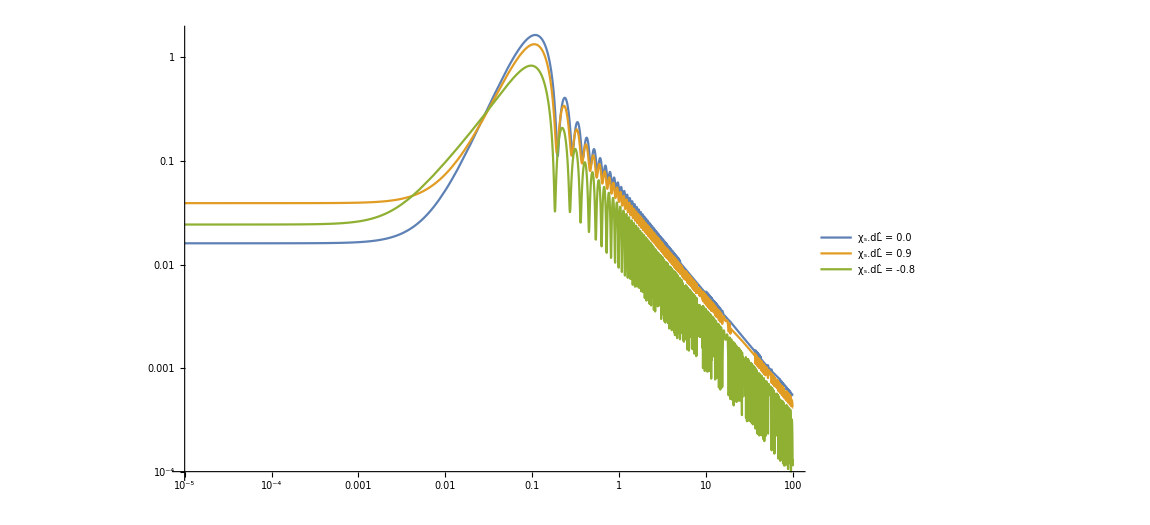

```mathematica
LogLogPlot[{Abs[PNfSpin[ResS0Coeff, 7, -35.0, 35.0]]/.f-> x, Abs[PNfSpin[ResS0p9Coeff, 7, -35.0, 35.0]]/.f-> x,Abs[PNfSpin[ResSm0p8Coeff, 7, -35.0, 35.0]]/.f-> x}, {x, 0.00001, 100},PlotLegends->Placed[{"χ_s.dL̂ = 0.0 ", "χ_s.dL̂ = 0.9 ","χ_s.dL̂ = -0.8 "},{0.850,0.7}],WorkingPrecision->50]
```

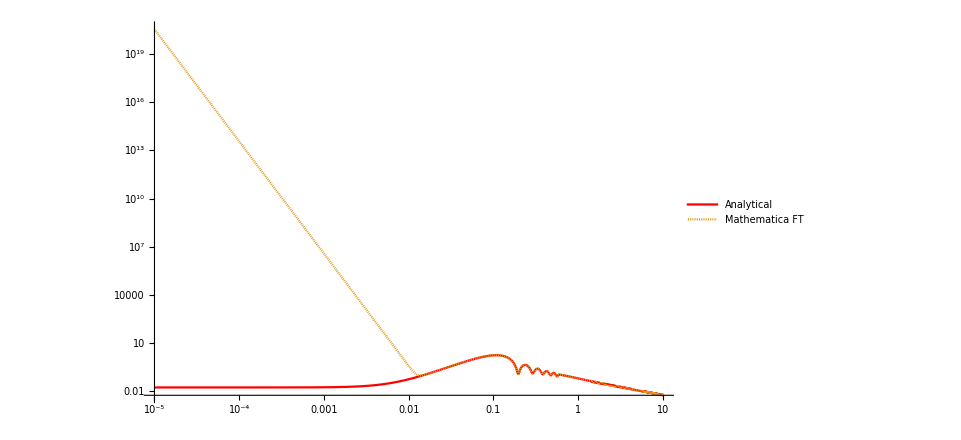

```mathematica
LogLogPlot[{Abs[PNfSpin[ResS0Coeff, 7, -35.0, 35.0]]/.f-> x, Sqrt[Abs[FTS0I1[ω]]]/. ω-> x}, {x, 0.00001, 10.1},PlotStyle-> {Red, Dashing[0.001]},PlotLegends->Placed[{"Analytical", "Mathematica FT"},{0.850,0.7}], WorkingPrecision->50]
```

```mathematica
Limit[Abs[PNfSpin[ResS0Coeff, 7, -35.0, 35.0]], f-> 0.000001]
```

1.94257×10^19

```mathematica
C0 = Cf[f, 0];C1 = Cf[f, 1];C2 = Cf[f, 2];C3 = Cf[f, 3];C4 = Cf[f, 4];C5 = Cf[f, 5];C6 = Cf[f, 6];C7 = Cf[f, 7];
```

```mathematica
LogLogPlot[{Abs[C0],Abs[C1], Abs[C2], Abs[C3], Abs[C7]}, {f, 0.0001, 100}, PlotLegends->Placed[{"FT[x^0]", "FT[x^1]","FT[x^2]","FT[x^3]", "FT[x^7]" },{1.0,0.8}],PlotStyle-> {Red, Green, Yellow, Blue, Black}, WorkingPrecision->40]
```

-Graphics-

```mathematica
C80 = Abs[Cf[f, 80]];C20 = Abs[Cf[f, 20]];
```

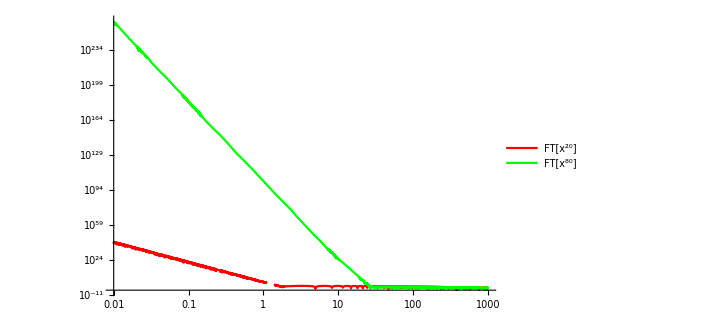

```mathematica
LogLogPlot[{C20, C80}, {f, 0.01, 1000.001},PlotStyle-> {Red, Green},PlotLegends->Placed[{"FT[x^20]", "FT[x^80]"},{0.850,0.7}], WorkingPrecision->MachinePrecision]
```

```mathematica
C10 = Cf[f, 10];C12 = Cf[f, 12];
```

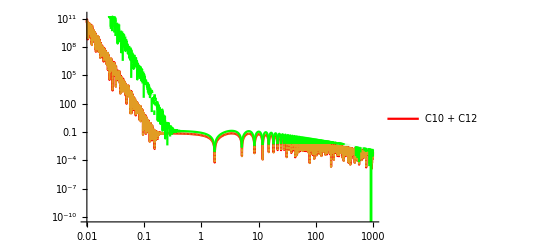

```mathematica
LogLogPlot[{Abs[C10],Abs[C10], Abs[C10 + C12]}, {f, 0.01, 1000.001},PlotStyle-> {Red, Dashing[0.00001], Green},PlotLegends->Placed[{"C10 + C12"},{0.850,0.7}]]
```

```mathematica
cst = SetPrecision[0.2, 40]
```

0.2000000000000000111022302462515654042363

```mathematica
LogLogPlot[{Abs[cst C0+ C1+ C2+C3], Abs[C7]}, {f, 0.0001, 100}, PlotLegends->Placed[{"FT[x^0]+FT[x^1]+FT[x^2]+FT[x^3]", "FT[x^7]" },{1.0,0.8}],PlotStyle-> {Red, Green}, WorkingPrecision->40]
```

-Graphics-